```mathematica
(* {βmax, Maximum Saturated Value LN12, Ω=ω } *)
Data={
{0.354148,0.12309578893436979, 1},
{0.5069545,0.44379035411366674, 2},
{0.6200005,0.5721371410281589, 3},
{0.7148825,0.6438034922922456, 4},
{0.7997935,0.6899651334110246, 5},
{0.8741555,0.7222888801749265, 6},
{0.9431125,0.7462244321884924, 7},
{1.0100005,0.764677157661628, 8}
};
```

```mathematica
(* 3D Plot the Data *)
ListPointPlot3D[Data, BoxRatios->{1, 1, 1}, AxesLabel->{"βmax", "Saturated ℒ𝒩_12", "Ω=ω"}, LabelStyle->Directive[12],  BaseStyle->"Latin Modern Roman", ImageSize->{300, 300}, ViewPoint->{1.2, -2.3, 1.5}]
```

-Graphics3D-

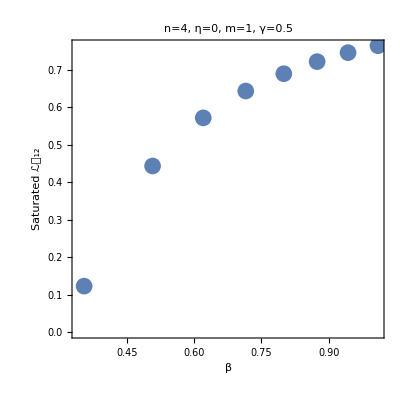
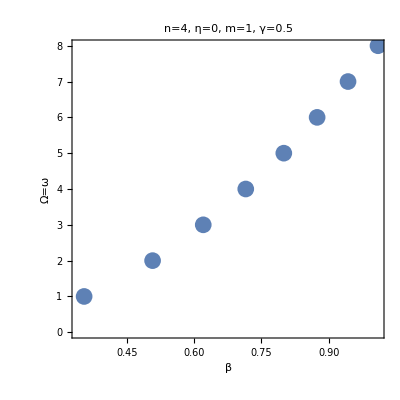
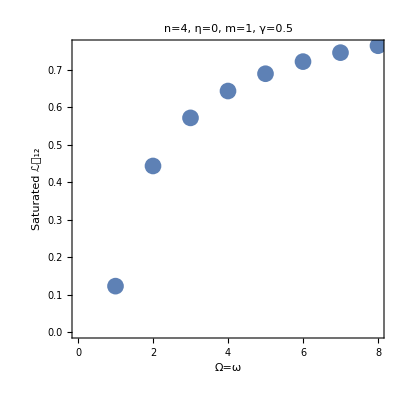

```mathematica
(* Plotting Properties *)
width=300;
height=300;
PlotFormat1={LabelStyle->Directive[12], BaseStyle->"Latin Modern Roman", ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width, Joined->False, PlotStyle->Directive[PointSize->0.03]};
LabelingInfo1={Frame->True, FrameLabel->{"β", "Saturated ℒ𝒩_12"}, PlotLabel->"n=4, η=0, m=1, γ=0.5"};
LabelingInfo2={Frame->True, FrameLabel->{"β", "Ω=ω"}, PlotLabel->"n=4, η=0, m=1, γ=0.5"};
LabelingInfo3={Frame->True, FrameLabel->{"Ω=ω", "Saturated ℒ𝒩_12"}, PlotLabel->"n=4, η=0, m=1, γ=0.5"};

(* {βmax, LN12} *)
BetaLN12=Table[{Data[[pt]][[1]], Data[[pt]][[2]]}, {pt, 1, Length[Data]}];
(* {βmax, Ω=ω} *)
BetaOomega=Table[{Data[[pt]][[1]], Data[[pt]][[3]]}, {pt, 1, Length[Data]}];
(* {Ω=ω, LN12} *)
LN12Oomega=Table[{Data[[pt]][[3]], Data[[pt]][[2]]}, {pt, 1, Length[Data]}];
(* Display Results *)
Row[{ListPlot[BetaLN12, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]], ListPlot[BetaOomega, Evaluate[PlotFormat1], Evaluate[LabelingInfo2]], ListPlot[LN12Oomega, Evaluate[PlotFormat1], Evaluate[LabelingInfo3]]}]
```

```mathematica
percentdiff[value1_, value2_]:=Abs[value1-value2]/Mean[{value1, value2}]*100
```

```mathematica
(* Modeling Functions *)
ifunc1=NonlinearModelFit[BetaLN12, a*Log[b*x^(1/10)+c],{a, b, c}, x];
ifunc2=NonlinearModelFit[BetaOomega, a*x^2+b*x+c,{a, b, c}, x];
ifunc3=NonlinearModelFit[LN12Oomega, a*Log[b*x^(1/10)+c],{a, b, c}, x];
```

```mathematica
plot1=Show[{ListPlot[BetaLN12, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]], Plot[ifunc1[x], {x, 0.35, 1.02}, PlotRange->All, PlotStyle->Directive[Dashed, Black]]}];
plot2=Show[{ListPlot[BetaOomega, Evaluate[PlotFormat1], Evaluate[LabelingInfo2]], Plot[ifunc2[x], {x, 0.35, 1.02}, PlotRange->All, PlotStyle->Directive[Dashed, Black]]}];
plot3=Show[{ListPlot[LN12Oomega, Evaluate[PlotFormat1], Evaluate[LabelingInfo3]], Plot[ifunc3[x], {x, 1, 8}, PlotRange->All, PlotStyle->Directive[Dashed, Black]]}];
```

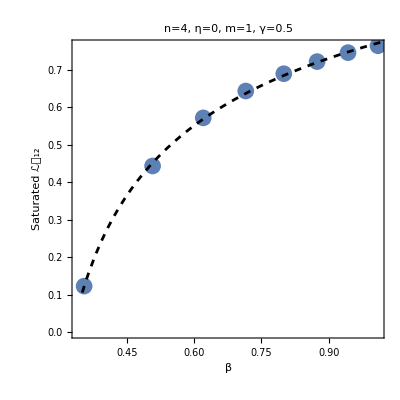
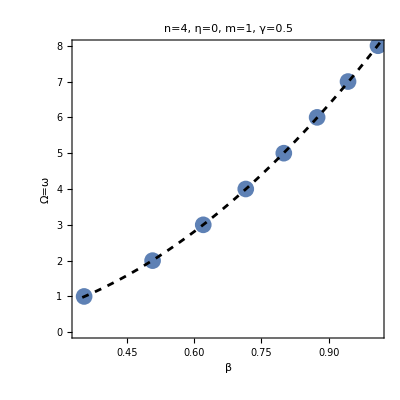
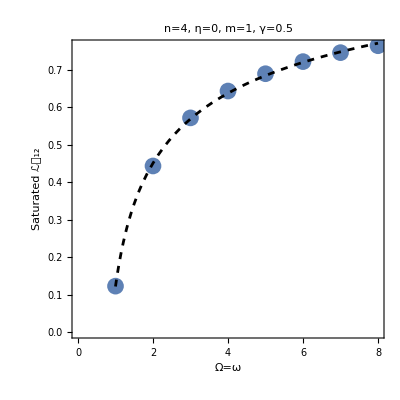
FittedModel[…]
{ | Estimate | Standard Error | t-Statistic | P-Value
a | 0.440264 | 0.0252505 | 17.4359 | 0.0000113736
b | 44.7352 | 5.32839 | 8.39562 | 0.000392817
c | -39.0049 | 4.78838 | -8.14575 | 0.000452856}
-Graphics-FittedModel[…]
{ | Estimate | Standard Error | t-Statistic | P-Value
a | 8.08392 | 0.11637 | 69.4675 | 1.17066×10^-8
b | -0.320555 | 0.161637 | -1.98318 | 0.104154
c | 0.0939045 | 0.0525588 | 1.78666 | 0.134041}
-Graphics-FittedModel[…]
{ | Estimate | Standard Error | t-Statistic | P-Value
a | 0.392293 | 0.0191787 | 20.4546 | 5.16765×10^-6
b | 25.0081 | 2.71211 | 9.22091 | 0.000251889
c | -23.6427 | 2.69787 | -8.76348 | 0.000320748}
-Graphics-

```mathematica
Row[{Column[{ifunc1, ifunc1[{"ParameterTable"}], plot1}], Column[{ifunc2, ifunc2[{"ParameterTable"}], plot2}], Column[{ifunc3, ifunc3[{"ParameterTable"}], plot3}]}]
```

```mathematica
Column[{"Simulated and Fitting Function % Difference",
Row[{MatrixForm[Table[percentdiff[BetaLN12[[i]][[2]], ifunc1[x]/.x->(BetaLN12[[i]][[1]])], {i, 1, Length[BetaLN12]}]], MatrixForm[Table[percentdiff[BetaOomega[[i]][[2]], ifunc2[x]/.x->(BetaOomega[[i]][[1]])], {i, 1, Length[BetaOomega]}]],
MatrixForm[Table[percentdiff[LN12Oomega[[i]][[2]], ifunc3[x]/.x->(LN12Oomega[[i]][[1]])], {i, 1, Length[LN12Oomega]}]]}]}]
```

Simulated and Fitting Function % Difference
(0.859167
1.84817
0.538931
0.998421
0.686234
0.30337
0.244411
0.953488)(0.574441
0.44837
0.0873913
0.0978608
0.171109
0.150163
0.25869
0.206726)(0.765742
1.69808
0.480094
0.92038
0.724773
0.271604
0.286725
0.882233)

Finding: βmax allows you to reach the saturated LN12 value faster or in the shortest amount of time. You can have β < βmax, and still reach the saturated the same LN12 value for each increase in ω = Ω, but it takes longer to do so, i.e. - the curve reaches it saturation value slower. For β > βmax, the saturated LN12 value starts to decrease. Therefore, βmax is the largest environmental coupling the system can handle before there are diminishing returns.

```mathematica
Table[{omega, ifunc3[omega]}, {omega, 1, 8}]
```

{{1,0.122157},{2,0.451391},{3,0.569397},{4,0.637905},{5,0.684983},{6,0.72033},{7,0.748367},{8,0.771453}}